# Project Euler Problem 46

## Goldbach’s other conjecture

It was proposed by Christian Goldbach that every odd composite number can be written as the sum of a prime and twice a square.

9 = 7 + 2×12
15 = 7 + 2×22
21 = 3 + 2×32
25 = 7 + 2×32
27 = 19 + 2×22
33 = 31 + 2×12

It turns out that the conjecture was false.

What is the smallest odd composite that cannot be written as the sum of a prime and twice a square?

Composite number is non-prime number.

### PreviousPrime[]

```mathematica
Clear[PreviousPrime]
PreviousPrime[x_?(#>2&)]:=Module[
{res=If[x≥ 2,Floor[x],x]},
While[!PrimeQ[res]&&res≥ 2,res--];
res
]
```

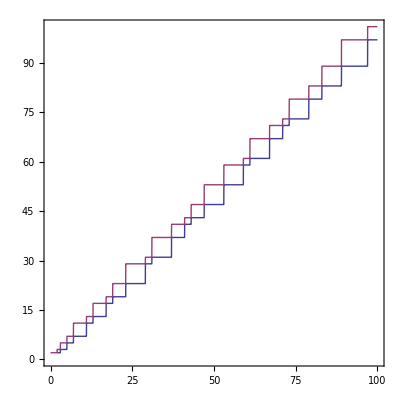

```mathematica
With[
{R=100},
Plot[
{
PreviousPrime[x],
NextPrime[x]
},
{x,0,R},
(*Filling-> Axis,*)
Frame-> True,
GridLines-> Table[Prime/@Range[R],{2}],
GridLinesStyle-> Directive[Dashed,LightGray],
AspectRatio-> 1,
PlotRangePadding-> 0
(*Joined-> True*)
]
]
```

```mathematica
$max=10000;
```

```mathematica
Complement[
Select[Range[Prime[$max],1,-2],!Prime[#]&],
Flatten@Table[Prime[idx]+2*Prime[Range[idx]]^2,{idx,Range[$max]}]
]
```

{}

```mathematica
n=1;
```

```mathematica
Flatten[{Table[a+2*b^2,{a,Prime/@Range[n]},{b,Range[n]}]}]
```